```mathematica
<<Graphs`
```

Evaluate IGDocumentation[] to get started.

Connected to cddlib via WSTP.

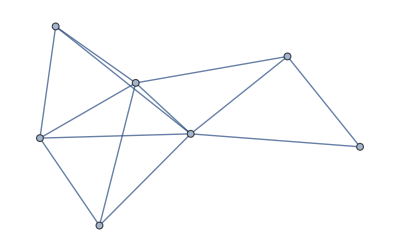

```mathematica
g=RandomGraph[{7,13}]
```

```mathematica
AbsoluteTiming[sol1=DeleteIsomorphicGraphs@SuperOrientationList[g];]
```

{57.1148,Null}

```mathematica
Length@sol1
```

531441

```mathematica
Export["input.g6",g]
```

input.g6

```mathematica
AbsoluteTiming[
sol=Import["output.txt","Table"];
sol=Drop[#,2]&/@sol;
sol2=Graph[DirectedEdge@@@Partition[#,2]]&/@sol;]
```

{63.4917,Null}

```mathematica
Length@sol2
```

531441

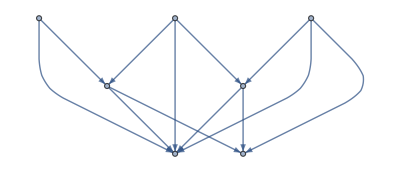

```mathematica
sol2[[1]]
```

```mathematica
sol1[[1]]
```

-Graphics-

```mathematica
sol1==sol2
```

False

```mathematica
Sort@sol1==Sort@sol2
```

$Aborted

```mathematica
AbsoluteTiming[
str=ToExpression@StringSplit@ReadList["outfile.txt",Record];
str=Drop[#,2]&/@str;
glist=Graph[DirectedEdge@@@Partition[#,2]]&/@str;]
```

{115.258,Null}

```mathematica
Length@glist
```

531441

```mathematica
AbsoluteTiming[str2=ToExpression@StringSplit@ReadList["output.txt",Record];]
```

{122.636,Null}

```mathematica
AbsoluteTiming[str1=Import["output.txt","Table"];]
```

{39.1334,Null}

```mathematica
str1==str2
```

True

```mathematica
l=ReadList["infile.txt",Number,RecordLists->True];//AbsoluteTiming
```

{4.45186,Null}

```mathematica
l[[1]]
```

{7,12,0,3,0,4,0,5,1,2,1,4,1,5,1,6,2,4,3,4,3,6,4,5,5,6}